```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
Pp[rt_,mt_,kt_]:=-4/3 rt-kt^2;
Qq[rt_,mt_,kt_]:=-mt^2/2+kt^3-4 kt rt;
xh[rt_,mt_,kt_]:=(-Qq[rt,mt,kt]+√(Qq[rt,mt,kt]^2+Pp[rt,mt,kt]^3))^(1/3);
z0[rt_,mt_,kt_]:=2 kt+xh[rt,mt,kt]-Pp[rt,mt,kt]/xh[rt,mt,kt];
e0[rt_,mt_,kt_]:=z0[rt,mt,kt]^(1/2);
app[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])+√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
apm[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])-√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
amp[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])+√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
amm[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])-√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
zerocheck[rt_,mt_,kt_]:=Simplify[app[rt,mt,kt]+apm[rt,mt,kt]+amp[rt,mt,kt]+amm[rt,mt,kt]]

a1[rt_,mt_,kt_]:=app[rt,mt,kt];
a2[rt_,mt_,kt_]:=apm[rt,mt,kt];
a3[rt_,mt_,kt_]:=amp[rt,mt,kt];
a4[rt_,mt_,kt_]:=amm[rt,mt,kt];
mm[rt_,mt_,kt_]:=((a2[rt,mt,kt]-a3[rt,mt,kt])(a1[rt,mt,kt]-a4[rt,mt,kt]))/((a1[rt,mt,kt]-a3[rt,mt,kt])(a2[rt,mt,kt]-a4[rt,mt,kt]));
rho[rt_,mt_,kt_,lam_]:=1/2 √(lam/3(a1[rt,mt,kt]-a3[rt,mt,kt])(a2[rt,mt,kt]-a4[rt,mt,kt]));
a[rt_,mt_,kt_,lam_,tau_]:=(a2[rt,mt,kt](a3[rt,mt,kt]-a1[rt,mt,kt])-a1[rt,mt,kt](a3[rt,mt,kt]-a2[rt,mt,kt])JacobiSN[rho[rt,mt,kt,lam] tau,mm[rt,mt,kt]]^2)/((a3[rt,mt,kt]-a1[rt,mt,kt])-(a3[rt,mt,kt]-a2[rt,mt,kt])JacobiSN[rho[rt,mt,kt,lam] tau,mm[rt,mt,kt]]^2)
tdS[rt_,mt_,kt_,lam_]:=-2 π ⅈ √(3/lam)
tgen[rt_,mt_,kt_,lam_]:=NIntegrate[a[rt,mt,kt,lam,tau]/tdS[rt,mt,kt,lam],{tau,0,-2ⅈ EllipticK[1-mm[rt,mt,kt]]/rho[rt,mt,kt,lam]},WorkingPrecision->6]
SdS[lam_]:=(24 π^2)/lam;
a12[rt_,mt_,kt_]:=a1[rt,mt,kt]-a2[rt,mt,kt];
a13[rt_,mt_,kt_]:=a1[rt,mt,kt]-a3[rt,mt,kt];
a14[rt_,mt_,kt_]:=a1[rt,mt,kt]-a4[rt,mt,kt];
a23[rt_,mt_,kt_]:=a2[rt,mt,kt]-a3[rt,mt,kt];
a24[rt_,mt_,kt_]:=a2[rt,mt,kt]-a4[rt,mt,kt];
a34[rt_,mt_,kt_]:=a3[rt,mt,kt]-a4[rt,mt,kt];
m0[rt_,mt_,kt_]:=(a12[rt,mt,kt] a34[rt,mt,kt])/(a13[rt,mt,kt] a24[rt,mt,kt]);
CK[rt_,mt_,kt_]:=a13[rt,mt,kt](a34[rt,mt,kt]^2-a12[rt,mt,kt]^2-4/3 a14[rt,mt,kt] a24[rt,mt,kt]);
CE[rt_,mt_,kt_]:=8 kt*(a13[rt,mt,kt] a24[rt,mt,kt])/a23[rt,mt,kt];
CPi[rt_,mt_,kt_]:=(a13[rt,mt,kt]^2-a24[rt,mt,kt]^2)(a14[rt,mt,kt]-a23[rt,mt,kt]);
Sanalytic[rt_,mt_,kt_]:=(2 π^2)/(24 π^2)(√3)/2*a23[rt,mt,kt]/(√(a13[rt,mt,kt] a24[rt,mt,kt]))(CK[rt,mt,kt]*EllipticK[m0[rt,mt,kt]]+CE[rt,mt,kt] EllipticE[m0[rt,mt,kt]]+CPi[rt,mt,kt] EllipticPi[a12[rt,mt,kt]/a13[rt,mt,kt],m0[rt,mt,kt]])
```

```mathematica
TdataClosed=Table[{10^RT,10^MT,Re[1/tgen[10^((4/3)RT),10^MT,1,1]]},{RT,-3/2,3,1/10.},{MT,-3/2,3,1/10.}];
```

```mathematica
TdataOpen=Table[{10^RT,10^MT,Re[1/tgen[10^((4/3)RT),10^MT,-1,1]]},{RT,-3/2,3,1/10.},{MT,-3/2,3,1/10.}];
```

-Graphics3D-

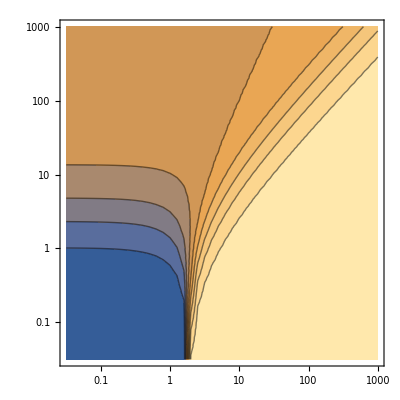

{RGBColor[0.2073209853520479, 0.36295610297335995, 0.5955545735836639],RGBColor[0.3481628722791146, 0.4260636292354716, 0.6144026565515749],RGBColor[0.5051453143392177, 0.48123317756330336, 0.5221190484395654],RGBColor[0.6621277563993208, 0.536402725891135, 0.4298354403275559],RGBColor[0.8191101984594235, 0.5915722742189667, 0.3375518322155466],RGBColor[0.9121553738849084, 0.650388434712271, 0.327681659043216],RGBColor[0.9372324413066501, 0.7130811032666251, 0.4054205680506151],RGBColor[0.9623095087283917, 0.7757737718209794, 0.4831594770580144],RGBColor[0.9873865761501335, 0.8384664403753337, 0.5608983860654136],RGBColor[1., 0.9098836594300003, 0.6747818614312506]}

{RGBColor[0.9121553738849084, 0.650388434712271, 0.327681659043216],RGBColor[0.9372324413066501, 0.7130811032666251, 0.4054205680506151],RGBColor[0.9623095087283917, 0.7757737718209794, 0.4831594770580144],RGBColor[0.9873865761501335, 0.8384664403753337, 0.5608983860654136],RGBColor[1., 0.9098836594300003, 0.6747818614312506]}

-Graphics3D-

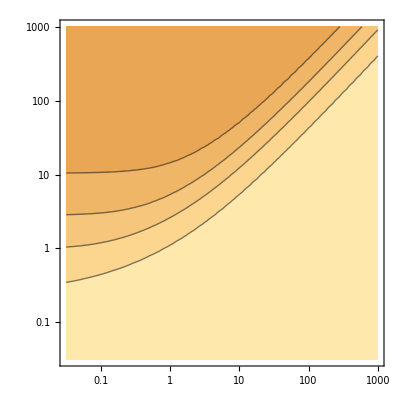

```mathematica
TplotOpen3D=ListPlot3D[Flatten[TdataOpen,1],ScalingFunctions->{"Log","Log",Identity},PlotRange->{{10^(-3/2),10^3},{10^(-3/2),10^3},{1,2}},Mesh->{{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1],Log[10^1.5],Log[10^2],Log[10^2.5],Log[10^3]},{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1],Log[10^1.5],Log[10^2],Log[10^2.5],Log[10^3]}}]
TplotOpenContour=ListContourPlot[Flatten[TdataOpen,1],ScalingFunctions->{"Log","Log",Identity},PlotRange->{{10^(-3/2),10^3},{10^(-3/2),10^3},{1,2}},Contours->{1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2}]
colorlist=Cases[TplotOpenContour[[1]],{___,clr_RGBColor,_GraphicsGroup}:>clr,All]
colorlistp={RGBColor[0.9121553738849084, 0.650388434712271, 0.327681659043216],RGBColor[0.9372324413066501, 0.7130811032666251, 0.4054205680506151],RGBColor[0.9623095087283917, 0.7757737718209794, 0.4831594770580144],RGBColor[0.9873865761501335, 0.8384664403753337, 0.5608983860654136],RGBColor[1., 0.9098836594300003, 0.6747818614312506]}
TplotClosed3D=ListPlot3D[Flatten[TdataClosed,1],ScalingFunctions->{"Log","Log",Identity},PlotRange->{{10^(-3/2),10^3},{10^(-3/2),10^3},{1,2}},Mesh->{{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1],Log[10^1.5],Log[10^2],Log[10^2.5],Log[10^3]},{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1],Log[10^1.5],Log[10^2],Log[10^2.5],Log[10^3]}}]
TplotClosedContour=ListContourPlot[Flatten[TdataClosed,1],ScalingFunctions->{"Log","Log",Identity},PlotRange->{{10^(-3/2),10^3},{10^(-3/2),10^3},{1,2}},Contours->{1.6,1.7,1.8,1.9,2},ContourShading->colorlistp]
```